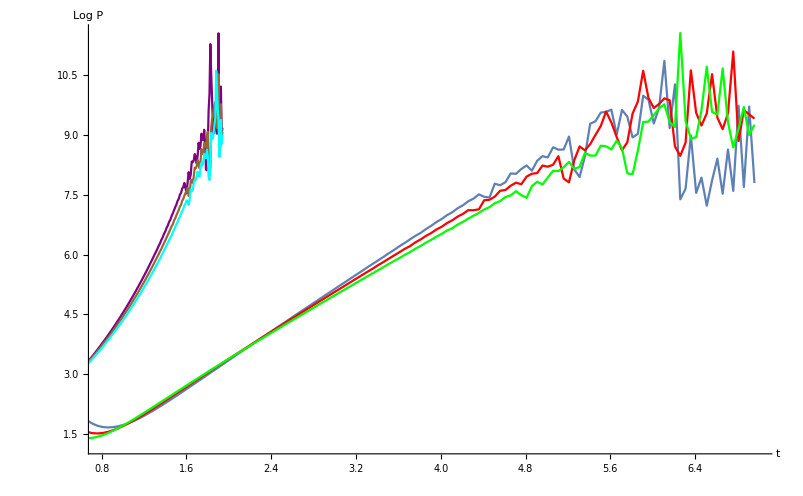

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]//Abs//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]//Abs//Log},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Abs//Log},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19]},{i,0.01,7,0.05}]//Abs//Log,PlotStyle->Purple],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.23],1,0.23,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.23],1,0.23]},{i,0.01,7,0.05}]//Abs//Log,PlotStyle->Brown],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245]},{i,0.01,7,0.05}]//Abs//Log,PlotStyle->Cyan],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,Log P}
]
]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%%%
```

Rough work on 20 May 2019

```mathematica
1. Data
```

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Table[{i,pz[i,0.9qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]},{i,0.01,5,0.05}]]
```

{{0.01,-111.683+0. ⅈ},{0.06,-371.268+0. ⅈ},{0.11,-259.023+0. ⅈ},{0.16,-145.664+0. ⅈ},{0.21,-83.0754+0. ⅈ},{0.26,-50.294+0. ⅈ},{0.31,-32.425+0. ⅈ},{0.36,-22.1396+0. ⅈ},{0.41,-15.9107+0. ⅈ},{0.46,-11.9715+0. ⅈ},{0.51,-9.39044+0. ⅈ},{0.56,-7.65087+0. ⅈ},{0.61,-6.4533+0. ⅈ},{0.66,-5.61697+0. ⅈ},{0.71,-5.02885+0. ⅈ},{0.76,-4.61603+0. ⅈ},{0.81,-4.33021+0. ⅈ},{0.86,-4.1384+0. ⅈ},{0.91,-4.01758+0. ⅈ},{0.96,-3.95128+0. ⅈ},{1.01,-3.9274+0. ⅈ},{1.06,-3.9369+0. ⅈ},{1.11,-3.97284+0. ⅈ},{1.16,-4.02982+0. ⅈ},{1.21,-4.10355+0. ⅈ},{1.26,-4.19061+0. ⅈ},{1.31,-4.2882+0. ⅈ},{1.36,-4.39406+0. ⅈ},{1.41,-4.50633+0. ⅈ},{1.46,-4.62352+0. ⅈ},{1.51,-4.74443+0. ⅈ},{1.56,-4.86811+0. ⅈ},{1.61,-4.99385+0. ⅈ},{1.66,-5.12113+0. ⅈ},{1.71,-5.24958+0. ⅈ},{1.76,-5.37903+0. ⅈ},{1.81,-5.50941+0. ⅈ},{1.86,-5.64083+0. ⅈ},{1.91,-5.77346+0. ⅈ},{1.96,-5.90762+0. ⅈ},{2.01,-6.04373+0. ⅈ},{2.06,-6.18227+0. ⅈ},{2.11,-6.32386+0. ⅈ},{2.16,-6.46916+0. ⅈ},{2.21,-6.61893+0. ⅈ},{2.26,-6.77407+0. ⅈ},{2.31,-6.93543+0. ⅈ},{2.36,-7.10414+0. ⅈ},{2.41,-7.2812+0. ⅈ},{2.46,-7.46791+0. ⅈ},{2.51,-7.66549+0. ⅈ},{2.56,-7.87539+0. ⅈ},{2.61,-8.0991+0. ⅈ},{2.66,-8.33827+0. ⅈ},{2.71,-8.59465+0. ⅈ},{2.76,-8.87014+0. ⅈ},{2.81,-9.16681+0. ⅈ},{2.86,-9.48685+0. ⅈ},{2.91,-9.83269+0. ⅈ},{2.96,-10.2069+0. ⅈ},{3.01,-10.6123+0. ⅈ},{3.06,-11.052+0. ⅈ},{3.11,-11.5292+0. ⅈ},{3.16,-12.0475+0. ⅈ},{3.21,-12.6109+0. ⅈ},{3.26,-13.2236+0. ⅈ},{3.31,-13.8901+0. ⅈ},{3.36,-14.6156+0. ⅈ},{3.41,-15.4054+0. ⅈ},{3.46,-16.2655+0. ⅈ},{3.51,-17.2023+0. ⅈ},{3.56,-18.2231+0. ⅈ},{3.61,-19.3353+0. ⅈ},{3.66,-20.5475+0. ⅈ},{3.71,-21.8687+0. ⅈ},{3.76,-23.3089+0. ⅈ},{3.81,-24.8791+0. ⅈ},{3.86,-26.591+0. ⅈ},{3.91,-28.4577+0. ⅈ},{3.96,-30.4931+0. ⅈ},{4.01,-32.7129+0. ⅈ},{4.06,-35.1334+0. ⅈ},{4.11,-37.7735+0. ⅈ},{4.16,-40.6528+0. ⅈ},{4.21,-43.7932+0. ⅈ},{4.26,-47.2187+0. ⅈ},{4.31,-50.9547+0. ⅈ},{4.36,-55.0303+0. ⅈ},{4.41,-59.4755+0. ⅈ},{4.46,-64.3249+0. ⅈ},{4.51,-69.6143+0. ⅈ},{4.56,-75.3848+0. ⅈ},{4.61,-81.6799+0. ⅈ},{4.66,-88.5465+0. ⅈ},{4.71,-96.0373+0. ⅈ},{4.76,-104.21+0. ⅈ},{4.81,-113.16+0. ⅈ},{4.86,-122.871+0. ⅈ},{4.91,-133.568+0. ⅈ},{4.96,-145.364+0. ⅈ}}

```mathematica
2. Plots: Increasing GB coupling shows decrease in size growth (as critical charge increases with GB coupling)
```

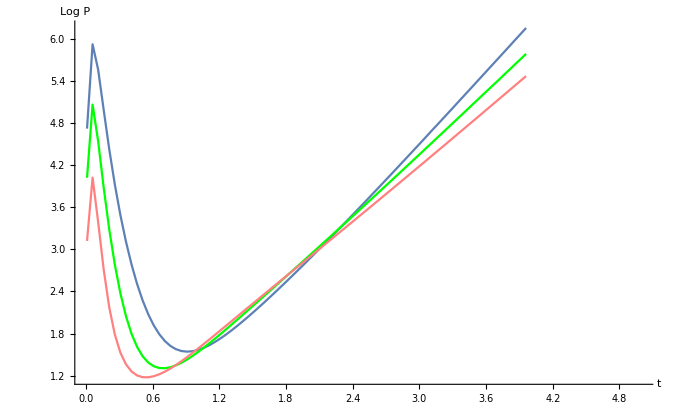

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,pz[i,0.8qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]//Abs//Log},{i,0.01,4,0.05}]],
ListLinePlot[Table[{i,pz[i,0.8qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,pz[i,0.8qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.24],1,0.24,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.24],1,0.24]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Pink],
PlotRange->{{0.0,5},All},AxesOrigin->{0.0,0},AxesLabel->{t,Log P}
]
]
```

```mathematica
3. Fixed GB coupling, increasing qcritical, stabilizes growth.
```

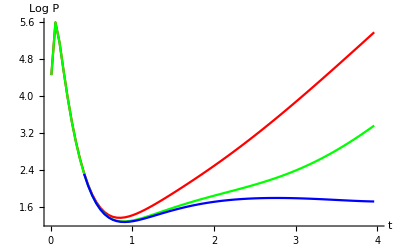

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,pz[i,0.85qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pz[i,0.9qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,pz[i,0.9069qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Blue],
PlotRange->{{0.0,4},All},AxesOrigin->{0.0,0},AxesLabel->{t,Log P}
]
]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%%
```

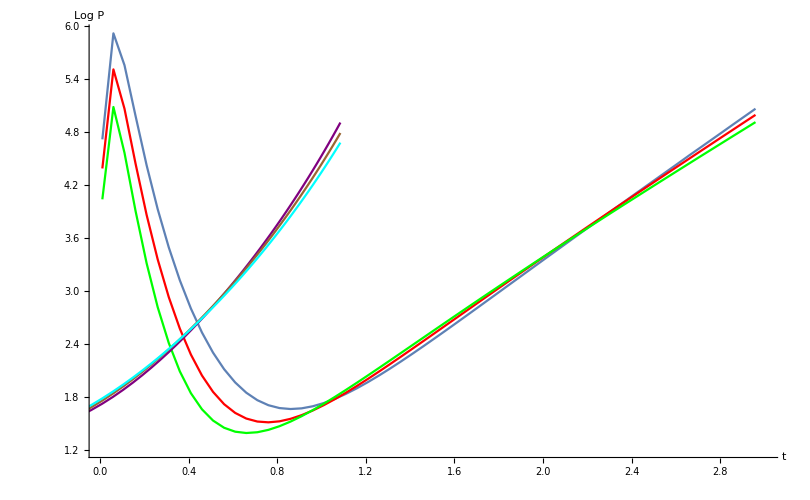

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]//Re//Abs//Log},{i,0.01,3,0.05}]],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]//Re//Abs//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Re//Abs//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19]},{i,0.01,3,0.05}]//Re//Abs//Log,PlotStyle->Purple],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.23],1,0.23,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.23],1,0.23]},{i,0.01,3,0.05}]//Re//Abs//Log,PlotStyle->Brown],
ListLinePlot[Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245]},{i,0.01,3,0.05}]//Re//Abs//Log,PlotStyle->Cyan],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AxesLabel->{t,Log P}
]
]
```

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]},{i,0.01,3,0.05}]];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Re},{i,0.01,3,0.05}]];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Re//Abs},{i,0.01,3,0.05}]];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Re//Abs//Log},{i,0.01,3,0.05}]];
]
```

{{0.01,-56.9159+0. ⅈ},{0.06,-161.795+0. ⅈ},{0.11,-96.378+0. ⅈ},{0.16,-49.9022+0. ⅈ},{0.21,-27.6097+0. ⅈ},{0.26,-16.801+0. ⅈ},{0.31,-11.2071+0. ⅈ},{0.36,-8.12635+0. ⅈ},{0.41,-6.34725+0. ⅈ},{0.46,-5.2897+0. ⅈ},{0.51,-4.65804+0. ⅈ},{0.56,-4.29343+0. ⅈ},{0.61,-4.10677+0. ⅈ},{0.66,-4.04628+0. ⅈ},{0.71,-4.08111+0. ⅈ},{0.76,-4.19255+0. ⅈ},{0.81,-4.36928+0. ⅈ},{0.86,-4.60451+0. ⅈ},{0.91,-4.89454+0. ⅈ},{0.96,-5.23756+0. ⅈ},{1.01,-5.63332+0. ⅈ},{1.06,-6.08254+0. ⅈ},{1.11,-6.58674+0. ⅈ},{1.16,-7.1482+0. ⅈ},{1.21,-7.76966+0. ⅈ},{1.26,-8.45445+0. ⅈ},{1.31,-9.20633+0. ⅈ},{1.36,-10.0296+0. ⅈ},{1.41,-10.929+0. ⅈ},{1.46,-11.9096+0. ⅈ},{1.51,-12.9772+0. ⅈ},{1.56,-14.138+0. ⅈ},{1.61,-15.3989+0. ⅈ},{1.66,-16.7669+0. ⅈ},{1.71,-18.2501+0. ⅈ},{1.76,-19.8569+0. ⅈ},{1.81,-21.597+0. ⅈ},{1.86,-23.4801+0. ⅈ},{1.91,-25.5174+0. ⅈ},{1.96,-27.7205+0. ⅈ},{2.01,-30.102+0. ⅈ},{2.06,-32.6755+0. ⅈ},{2.11,-35.4575+0. ⅈ},{2.16,-38.4613+0. ⅈ},{2.21,-41.6987+0. ⅈ},{2.26,-45.2125+0. ⅈ},{2.31,-49.0021+0. ⅈ},{2.36,-53.0897+0. ⅈ},{2.41,-57.4814+0. ⅈ},{2.46,-62.2453+0. ⅈ},{2.51,-67.3844+0. ⅈ},{2.56,-72.9222+0. ⅈ},{2.61,-78.9065+0. ⅈ},{2.66,-85.3593+0. ⅈ},{2.71,-92.3525+0. ⅈ},{2.76,-99.8379+0. ⅈ},{2.81,-107.945+0. ⅈ},{2.86,-116.702+0. ⅈ},{2.91,-126.131+0. ⅈ},{2.96,-136.328+0. ⅈ}}

{{0.01,-56.9159},{0.06,-161.795},{0.11,-96.378},{0.16,-49.9022},{0.21,-27.6097},{0.26,-16.801},{0.31,-11.2071},{0.36,-8.12635},{0.41,-6.34725},{0.46,-5.2897},{0.51,-4.65804},{0.56,-4.29343},{0.61,-4.10677},{0.66,-4.04628},{0.71,-4.08111},{0.76,-4.19255},{0.81,-4.36928},{0.86,-4.60451},{0.91,-4.89454},{0.96,-5.23756},{1.01,-5.63332},{1.06,-6.08254},{1.11,-6.58674},{1.16,-7.1482},{1.21,-7.76966},{1.26,-8.45445},{1.31,-9.20633},{1.36,-10.0296},{1.41,-10.929},{1.46,-11.9096},{1.51,-12.9772},{1.56,-14.138},{1.61,-15.3989},{1.66,-16.7669},{1.71,-18.2501},{1.76,-19.8569},{1.81,-21.597},{1.86,-23.4801},{1.91,-25.5174},{1.96,-27.7205},{2.01,-30.102},{2.06,-32.6755},{2.11,-35.4575},{2.16,-38.4613},{2.21,-41.6987},{2.26,-45.2125},{2.31,-49.0021},{2.36,-53.0897},{2.41,-57.4814},{2.46,-62.2453},{2.51,-67.3844},{2.56,-72.9222},{2.61,-78.9065},{2.66,-85.3593},{2.71,-92.3525},{2.76,-99.8379},{2.81,-107.945},{2.86,-116.702},{2.91,-126.131},{2.96,-136.328}}

{{0.01,56.9159},{0.06,161.795},{0.11,96.378},{0.16,49.9022},{0.21,27.6097},{0.26,16.801},{0.31,11.2071},{0.36,8.12635},{0.41,6.34725},{0.46,5.2897},{0.51,4.65804},{0.56,4.29343},{0.61,4.10677},{0.66,4.04628},{0.71,4.08111},{0.76,4.19255},{0.81,4.36928},{0.86,4.60451},{0.91,4.89454},{0.96,5.23756},{1.01,5.63332},{1.06,6.08254},{1.11,6.58674},{1.16,7.1482},{1.21,7.76966},{1.26,8.45445},{1.31,9.20633},{1.36,10.0296},{1.41,10.929},{1.46,11.9096},{1.51,12.9772},{1.56,14.138},{1.61,15.3989},{1.66,16.7669},{1.71,18.2501},{1.76,19.8569},{1.81,21.597},{1.86,23.4801},{1.91,25.5174},{1.96,27.7205},{2.01,30.102},{2.06,32.6755},{2.11,35.4575},{2.16,38.4613},{2.21,41.6987},{2.26,45.2125},{2.31,49.0021},{2.36,53.0897},{2.41,57.4814},{2.46,62.2453},{2.51,67.3844},{2.56,72.9222},{2.61,78.9065},{2.66,85.3593},{2.71,92.3525},{2.76,99.8379},{2.81,107.945},{2.86,116.702},{2.91,126.131},{2.96,136.328}}

{{0.01,4.04157},{0.06,5.08633},{0.11,4.56828},{0.16,3.91007},{0.21,3.31817},{0.26,2.82144},{0.31,2.41655},{0.36,2.09511},{0.41,1.84802},{0.46,1.66576},{0.51,1.53859},{0.56,1.45709},{0.61,1.41264},{0.66,1.3978},{0.71,1.40637},{0.76,1.43331},{0.81,1.4746},{0.86,1.52704},{0.91,1.58812},{0.96,1.65586},{1.01,1.7287},{1.06,1.80542},{1.11,1.88506},{1.16,1.96686},{1.21,2.05023},{1.26,2.13469},{1.31,2.21989},{1.36,2.30554},{1.41,2.39142},{1.46,2.47734},{1.51,2.56319},{1.56,2.64887},{1.61,2.73429},{1.66,2.81941},{1.71,2.90417},{1.76,2.98855},{1.81,3.07255},{1.86,3.15615},{1.91,3.23936},{1.96,3.32217},{2.01,3.40459},{2.06,3.48663},{2.11,3.56833},{2.16,3.64965},{2.21,3.73047},{2.26,3.81137},{2.31,3.89186},{2.36,3.97198},{2.41,4.05146},{2.46,4.13108},{2.51,4.21041},{2.56,4.28939},{2.61,4.36826},{2.66,4.44687},{2.71,4.52561},{2.76,4.60355},{2.81,4.68162},{2.86,4.75962},{2.91,4.83732},{2.96,4.91506}}

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]},{i,0.01,7,0.05}]];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Re},{i,0.01,7,0.05}]];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Re//Abs},{i,0.01,7,0.05}]];
Print[
Table[{i,pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]//Re//Abs//Log},{i,0.01,7,0.05}]];
]
```

{{0.01,-56.9159+0. ⅈ},{0.06,-161.795+0. ⅈ},{0.11,-96.378+0. ⅈ},{0.16,-49.9022+0. ⅈ},{0.21,-27.6097+0. ⅈ},{0.26,-16.801+0. ⅈ},{0.31,-11.2071+0. ⅈ},{0.36,-8.12635+0. ⅈ},{0.41,-6.34725+0. ⅈ},{0.46,-5.2897+0. ⅈ},{0.51,-4.65804+0. ⅈ},{0.56,-4.29343+0. ⅈ},{0.61,-4.10677+0. ⅈ},{0.66,-4.04628+0. ⅈ},{0.71,-4.08111+0. ⅈ},{0.76,-4.19255+0. ⅈ},{0.81,-4.36928+0. ⅈ},{0.86,-4.60451+0. ⅈ},{0.91,-4.89454+0. ⅈ},{0.96,-5.23756+0. ⅈ},{1.01,-5.63332+0. ⅈ},{1.06,-6.08254+0. ⅈ},{1.11,-6.58674+0. ⅈ},{1.16,-7.1482+0. ⅈ},{1.21,-7.76966+0. ⅈ},{1.26,-8.45445+0. ⅈ},{1.31,-9.20633+0. ⅈ},{1.36,-10.0296+0. ⅈ},{1.41,-10.929+0. ⅈ},{1.46,-11.9096+0. ⅈ},{1.51,-12.9772+0. ⅈ},{1.56,-14.138+0. ⅈ},{1.61,-15.3989+0. ⅈ},{1.66,-16.7669+0. ⅈ},{1.71,-18.2501+0. ⅈ},{1.76,-19.8569+0. ⅈ},{1.81,-21.597+0. ⅈ},{1.86,-23.4801+0. ⅈ},{1.91,-25.5174+0. ⅈ},{1.96,-27.7205+0. ⅈ},{2.01,-30.102+0. ⅈ},{2.06,-32.6755+0. ⅈ},{2.11,-35.4575+0. ⅈ},{2.16,-38.4613+0. ⅈ},{2.21,-41.6987+0. ⅈ},{2.26,-45.2125+0. ⅈ},{2.31,-49.0021+0. ⅈ},{2.36,-53.0897+0. ⅈ},{2.41,-57.4814+0. ⅈ},{2.46,-62.2453+0. ⅈ},{2.51,-67.3844+0. ⅈ},{2.56,-72.9222+0. ⅈ},{2.61,-78.9065+0. ⅈ},{2.66,-85.3593+0. ⅈ},{2.71,-92.3525+0. ⅈ},{2.76,-99.8379+0. ⅈ},{2.81,-107.945+0. ⅈ},{2.86,-116.702+0. ⅈ},{2.91,-126.131+0. ⅈ},{2.96,-136.328+0. ⅈ},{3.01,-147.295+0. ⅈ},{3.06,-159.146+0. ⅈ},{3.11,-171.962+0. ⅈ},{3.16,-185.73+0. ⅈ},{3.21,-200.614+0. ⅈ},{3.26,-216.67+0. ⅈ},{3.31,-233.967+0. ⅈ},{3.36,-252.696+0. ⅈ},{3.41,-272.816+0. ⅈ},{3.46,-294.542+0. ⅈ},{3.51,-318.369+0. ⅈ},{3.56,-343.319+0. ⅈ},{3.61,-368.842+0. ⅈ},{3.66,-399.806+0. ⅈ},{3.71,-428.363+0. ⅈ},{3.76,-465.805+0. ⅈ},{3.81,-500.153+0. ⅈ},{3.86,-542.777+0. ⅈ},{3.91,-581.717+0. ⅈ},{3.96,-632.201+0. ⅈ},{4.01,-676.707+0. ⅈ},{4.06,-736.298+0. ⅈ},{4.11,-778.928+0. ⅈ},{4.16,-853.703+0. ⅈ},{4.21,-914.284+0. ⅈ},{4.26,-990.852+0. ⅈ},{4.31,-1066.25+0. ⅈ},{4.36,-1145.42+0. ⅈ},{4.41,-1245.35+0. ⅈ},{4.46,-1321.42+0. ⅈ},{4.51,-1456.86+0. ⅈ},{4.56,-1532.7+0. ⅈ},{4.61,-1698.87+0. ⅈ},{4.66,-1774.43+0. ⅈ},{4.71,-1968.11+0. ⅈ},{4.76,-1782.97+0. ⅈ},{4.81,-1668.61+0. ⅈ},{4.86,-2237.74+0. ⅈ},{4.91,-2495.52+0. ⅈ},{4.96,-2327.78+0. ⅈ},{5.01,-2771.24+0. ⅈ},{5.06,-3285.2+0. ⅈ},{5.11,-3255.03+0. ⅈ},{5.16,-3590.54+0. ⅈ},{5.21,-4104.99+0. ⅈ},{5.26,-3449.16+0. ⅈ},{5.31,-3610.61+0. ⅈ},{5.36,-5132.55+0. ⅈ},{5.41,-4813.43+0. ⅈ},{5.46,-4797.89+0. ⅈ},{5.51,-6153.27+0. ⅈ},{5.56,-6058.26+0. ⅈ},{5.61,-5602.81+0. ⅈ},{5.66,-6987.68+0. ⅈ},{5.71,-5796.54+0. ⅈ},{5.76,-3086.16+0. ⅈ},{5.81,-3004.68+0. ⅈ},{5.86,-5440.49+0. ⅈ},{5.91,-11125.6+0. ⅈ},{5.96,-11270.6+0. ⅈ},{6.01,-13239.7+0. ⅈ},{6.06,-15648.7+0. ⅈ},{6.11,-17352.6+0. ⅈ},{6.16,0.+11079.1 ⅈ},{6.21,0.+9821.87 ⅈ},{6.26,-103365.+0. ⅈ},{6.31,-11539.-0.000448532 ⅈ},{6.36,-7324.11-0.000537335 ⅈ},{6.41,-7638.49-0.000596374 ⅈ},{6.46,-15002.-0.000247306 ⅈ},{6.51,-44470.7+0.00905946 ⅈ},{6.56,-0.00455213-14357.9 ⅈ},{6.61,-0.0055982-13374.9 ⅈ},{6.66,-0.232214-42668.4 ⅈ},{6.71,-0.00169714-11100.7 ⅈ},{6.76,-0.0012619+5878.3 ⅈ},{6.81,-0.00596653-9450.5 ⅈ},{6.86,-16214.9-0.0832017 ⅈ},{6.91,-8049.78-0.0222781 ⅈ},{6.96,-10395.-0.0271695 ⅈ}}

{{0.01,-56.9159},{0.06,-161.795},{0.11,-96.378},{0.16,-49.9022},{0.21,-27.6097},{0.26,-16.801},{0.31,-11.2071},{0.36,-8.12635},{0.41,-6.34725},{0.46,-5.2897},{0.51,-4.65804},{0.56,-4.29343},{0.61,-4.10677},{0.66,-4.04628},{0.71,-4.08111},{0.76,-4.19255},{0.81,-4.36928},{0.86,-4.60451},{0.91,-4.89454},{0.96,-5.23756},{1.01,-5.63332},{1.06,-6.08254},{1.11,-6.58674},{1.16,-7.1482},{1.21,-7.76966},{1.26,-8.45445},{1.31,-9.20633},{1.36,-10.0296},{1.41,-10.929},{1.46,-11.9096},{1.51,-12.9772},{1.56,-14.138},{1.61,-15.3989},{1.66,-16.7669},{1.71,-18.2501},{1.76,-19.8569},{1.81,-21.597},{1.86,-23.4801},{1.91,-25.5174},{1.96,-27.7205},{2.01,-30.102},{2.06,-32.6755},{2.11,-35.4575},{2.16,-38.4613},{2.21,-41.6987},{2.26,-45.2125},{2.31,-49.0021},{2.36,-53.0897},{2.41,-57.4814},{2.46,-62.2453},{2.51,-67.3844},{2.56,-72.9222},{2.61,-78.9065},{2.66,-85.3593},{2.71,-92.3525},{2.76,-99.8379},{2.81,-107.945},{2.86,-116.702},{2.91,-126.131},{2.96,-136.328},{3.01,-147.295},{3.06,-159.146},{3.11,-171.962},{3.16,-185.73},{3.21,-200.614},{3.26,-216.67},{3.31,-233.967},{3.36,-252.696},{3.41,-272.816},{3.46,-294.542},{3.51,-318.369},{3.56,-343.319},{3.61,-368.842},{3.66,-399.806},{3.71,-428.363},{3.76,-465.805},{3.81,-500.153},{3.86,-542.777},{3.91,-581.717},{3.96,-632.201},{4.01,-676.707},{4.06,-736.298},{4.11,-778.928},{4.16,-853.703},{4.21,-914.284},{4.26,-990.852},{4.31,-1066.25},{4.36,-1145.42},{4.41,-1245.35},{4.46,-1321.42},{4.51,-1456.86},{4.56,-1532.7},{4.61,-1698.87},{4.66,-1774.43},{4.71,-1968.11},{4.76,-1782.97},{4.81,-1668.61},{4.86,-2237.74},{4.91,-2495.52},{4.96,-2327.78},{5.01,-2771.24},{5.06,-3285.2},{5.11,-3255.03},{5.16,-3590.54},{5.21,-4104.99},{5.26,-3449.16},{5.31,-3610.61},{5.36,-5132.55},{5.41,-4813.43},{5.46,-4797.89},{5.51,-6153.27},{5.56,-6058.26},{5.61,-5602.81},{5.66,-6987.68},{5.71,-5796.54},{5.76,-3086.16},{5.81,-3004.68},{5.86,-5440.49},{5.91,-11125.6},{5.96,-11270.6},{6.01,-13239.7},{6.06,-15648.7},{6.11,-17352.6},{6.16,0.},{6.21,0.},{6.26,-103365.},{6.31,-11539.},{6.36,-7324.11},{6.41,-7638.49},{6.46,-15002.},{6.51,-44470.7},{6.56,-0.00455213},{6.61,-0.0055982},{6.66,-0.232214},{6.71,-0.00169714},{6.76,-0.0012619},{6.81,-0.00596653},{6.86,-16214.9},{6.91,-8049.78},{6.96,-10395.}}

{{0.01,56.9159},{0.06,161.795},{0.11,96.378},{0.16,49.9022},{0.21,27.6097},{0.26,16.801},{0.31,11.2071},{0.36,8.12635},{0.41,6.34725},{0.46,5.2897},{0.51,4.65804},{0.56,4.29343},{0.61,4.10677},{0.66,4.04628},{0.71,4.08111},{0.76,4.19255},{0.81,4.36928},{0.86,4.60451},{0.91,4.89454},{0.96,5.23756},{1.01,5.63332},{1.06,6.08254},{1.11,6.58674},{1.16,7.1482},{1.21,7.76966},{1.26,8.45445},{1.31,9.20633},{1.36,10.0296},{1.41,10.929},{1.46,11.9096},{1.51,12.9772},{1.56,14.138},{1.61,15.3989},{1.66,16.7669},{1.71,18.2501},{1.76,19.8569},{1.81,21.597},{1.86,23.4801},{1.91,25.5174},{1.96,27.7205},{2.01,30.102},{2.06,32.6755},{2.11,35.4575},{2.16,38.4613},{2.21,41.6987},{2.26,45.2125},{2.31,49.0021},{2.36,53.0897},{2.41,57.4814},{2.46,62.2453},{2.51,67.3844},{2.56,72.9222},{2.61,78.9065},{2.66,85.3593},{2.71,92.3525},{2.76,99.8379},{2.81,107.945},{2.86,116.702},{2.91,126.131},{2.96,136.328},{3.01,147.295},{3.06,159.146},{3.11,171.962},{3.16,185.73},{3.21,200.614},{3.26,216.67},{3.31,233.967},{3.36,252.696},{3.41,272.816},{3.46,294.542},{3.51,318.369},{3.56,343.319},{3.61,368.842},{3.66,399.806},{3.71,428.363},{3.76,465.805},{3.81,500.153},{3.86,542.777},{3.91,581.717},{3.96,632.201},{4.01,676.707},{4.06,736.298},{4.11,778.928},{4.16,853.703},{4.21,914.284},{4.26,990.852},{4.31,1066.25},{4.36,1145.42},{4.41,1245.35},{4.46,1321.42},{4.51,1456.86},{4.56,1532.7},{4.61,1698.87},{4.66,1774.43},{4.71,1968.11},{4.76,1782.97},{4.81,1668.61},{4.86,2237.74},{4.91,2495.52},{4.96,2327.78},{5.01,2771.24},{5.06,3285.2},{5.11,3255.03},{5.16,3590.54},{5.21,4104.99},{5.26,3449.16},{5.31,3610.61},{5.36,5132.55},{5.41,4813.43},{5.46,4797.89},{5.51,6153.27},{5.56,6058.26},{5.61,5602.81},{5.66,6987.68},{5.71,5796.54},{5.76,3086.16},{5.81,3004.68},{5.86,5440.49},{5.91,11125.6},{5.96,11270.6},{6.01,13239.7},{6.06,15648.7},{6.11,17352.6},{6.16,0.},{6.21,0.},{6.26,103365.},{6.31,11539.},{6.36,7324.11},{6.41,7638.49},{6.46,15002.},{6.51,44470.7},{6.56,0.00455213},{6.61,0.0055982},{6.66,0.232214},{6.71,0.00169714},{6.76,0.0012619},{6.81,0.00596653},{6.86,16214.9},{6.91,8049.78},{6.96,10395.}}

{{0.01,4.04157},{0.06,5.08633},{0.11,4.56828},{0.16,3.91007},{0.21,3.31817},{0.26,2.82144},{0.31,2.41655},{0.36,2.09511},{0.41,1.84802},{0.46,1.66576},{0.51,1.53859},{0.56,1.45709},{0.61,1.41264},{0.66,1.3978},{0.71,1.40637},{0.76,1.43331},{0.81,1.4746},{0.86,1.52704},{0.91,1.58812},{0.96,1.65586},{1.01,1.7287},{1.06,1.80542},{1.11,1.88506},{1.16,1.96686},{1.21,2.05023},{1.26,2.13469},{1.31,2.21989},{1.36,2.30554},{1.41,2.39142},{1.46,2.47734},{1.51,2.56319},{1.56,2.64887},{1.61,2.73429},{1.66,2.81941},{1.71,2.90417},{1.76,2.98855},{1.81,3.07255},{1.86,3.15615},{1.91,3.23936},{1.96,3.32217},{2.01,3.40459},{2.06,3.48663},{2.11,3.56833},{2.16,3.64965},{2.21,3.73047},{2.26,3.81137},{2.31,3.89186},{2.36,3.97198},{2.41,4.05146},{2.46,4.13108},{2.51,4.21041},{2.56,4.28939},{2.61,4.36826},{2.66,4.44687},{2.71,4.52561},{2.76,4.60355},{2.81,4.68162},{2.86,4.75962},{2.91,4.83732},{2.96,4.91506},{3.01,4.99244},{3.06,5.06982},{3.11,5.14727},{3.16,5.22429},{3.21,5.30138},{3.26,5.37838},{3.31,5.45518},{3.36,5.53219},{3.41,5.6088},{3.46,5.68542},{3.51,5.76321},{3.56,5.83866},{3.61,5.91037},{3.66,5.99098},{3.71,6.05997},{3.76,6.14377},{3.81,6.21491},{3.86,6.2967},{3.91,6.36598},{3.96,6.44921},{4.01,6.51724},{4.06,6.60163},{4.11,6.65792},{4.16,6.74958},{4.21,6.81814},{4.26,6.89857},{4.31,6.9719},{4.36,7.04353},{4.41,7.12717},{4.46,7.18646},{4.51,7.28404},{4.56,7.33479},{4.61,7.43772},{4.66,7.48124},{4.71,7.58483},{4.76,7.48604},{4.81,7.41975},{4.86,7.71322},{4.91,7.82225},{4.96,7.75267},{5.01,7.92705},{5.06,8.09718},{5.11,8.08796},{5.16,8.18606},{5.21,8.31996},{5.26,8.14589},{5.31,8.19163},{5.36,8.54336},{5.41,8.47916},{5.46,8.47593},{5.51,8.72474},{5.56,8.70918},{5.61,8.63102},{5.66,8.8519},{5.71,8.66502},{5.76,8.03468},{5.81,8.00793},{5.86,8.60162},{5.91,9.31701},{5.96,9.32996},{6.01,9.49097},{6.06,9.65814},{6.11,9.7615},{6.16,Indeterminate},{6.21,Indeterminate},{6.26,11.546},{6.31,9.35349},{6.36,8.89893},{6.41,8.94095},{6.46,9.61594},{6.51,10.7026},{6.56,-5.39216},{6.61,-5.18531},{6.66,-1.4601},{6.71,-6.37881},{6.76,-6.67514},{6.81,-5.12159},{6.86,9.69368},{6.91,8.9934},{6.96,9.24908}}

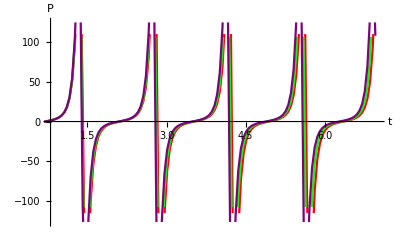

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.13],1,0.13,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.13],1,0.13]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.14],1,0.14,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.14],1,0.14]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,P}
]
]
```

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Print[Table[{i,pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12]},{i,0.01,7,0.05}]];
Print[Table[{i,Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12]]},{i,0.01,7,0.05}]];
]
```

{{0.01,-79.9569},{0.06,-248.96},{0.11,-160.81},{0.16,-85.421},{0.21,-46.5112},{0.26,-26.9321},{0.31,-16.5467},{0.36,-10.6775},{0.41,-7.15027},{0.46,-4.8991},{0.51,-3.36912},{0.56,-2.25452},{0.61,-1.37811},{0.66,-0.633313},{0.71,0.0494192},{0.76,0.737316},{0.81,1.49655},{0.86,2.39999},{0.91,3.56224},{0.96,5.17476},{1.01,7.57019},{1.06,11.357},{1.11,17.7142},{1.16,29.0679},{1.21,50.6668},{1.26,93.7768},{1.31,175.401},{1.36,250.576},{1.41,21.7},{1.46,-247.28},{1.51,-186.29},{1.56,-100.369},{1.61,-53.9523},{1.66,-30.7448},{1.71,-18.6236},{1.76,-11.8821},{1.81,-7.89231},{1.86,-5.38457},{1.91,-3.70796},{1.96,-2.50872},{2.01,-1.58421},{2.06,-0.813579},{2.11,-0.121059},{2.16,0.558845},{2.21,1.29407},{2.26,2.15233},{2.31,3.23476},{2.36,4.709},{2.41,6.86296},{2.46,10.2161},{2.51,15.76},{2.56,25.5046},{2.61,43.7536},{2.66,79.8759},{2.71,150.705},{2.76,244.245},{2.81,118.898},{2.86,-220.244},{2.91,-212.228},{2.96,-118.032},{3.01,-62.8316},{3.06,-35.2363},{3.11,-21.0311},{3.16,-13.2569},{3.21,-8.72646},{3.26,-5.92191},{3.31,-4.07668},{3.36,-2.78012},{3.41,-1.79994},{3.46,-0.998789},{3.51,-0.2924},{3.56,0.383972},{3.61,1.09931},{3.66,1.91873},{3.71,2.93184},{3.76,4.28573},{3.81,6.23042},{3.86,9.21098},{3.91,14.0646},{3.96,22.4626},{4.01,37.9394},{4.06,68.2191},{4.11,128.576},{4.16,225.07},{4.21,193.354},{4.26,-162.007},{4.31,-235.172},{4.36,-138.619},{4.41,-73.44},{4.46,-40.5479},{4.51,-23.8332},{4.56,-14.8318},{4.61,-9.66773},{4.66,-6.51905},{4.71,-4.47972},{4.76,-3.07134},{4.81,-2.02688},{4.86,-1.18995},{4.91,-0.465761},{4.96,0.2117},{5.01,0.911078},{5.06,1.69727},{5.11,2.65028},{5.16,3.89943},{5.21,5.66247},{5.26,8.32212},{5.31,12.5879},{5.36,19.8549},{5.41,33.0329},{5.46,58.4626},{5.51,109.376},{5.56,200.153},{5.61,236.61},{5.66,-75.1116},{5.71,-249.339},{5.76,-162.038},{5.81,-86.1066},{5.86,-46.852},{5.91,-27.108},{5.96,-16.6433},{6.01,-10.7339},{6.06,-7.18528},{6.11,-4.92218},{6.16,-3.38535},{6.21,-2.26681},{6.26,-1.38817},{6.31,-0.64219},{6.36,0.04093},{6.41,0.728328},{6.46,1.48627},{6.51,2.38729},{6.56,3.5453},{6.61,5.15047},{6.66,7.53305},{6.71,11.2967},{6.76,17.6102},{6.81,28.8767},{6.86,50.2935},{6.91,93.0266},{6.96,174.125}}

{{0.01,-79.9569},{0.06,-248.96},{0.11,-160.81},{0.16,-85.421},{0.21,-46.5112},{0.26,-26.9321},{0.31,-16.5467},{0.36,-10.6775},{0.41,-7.15027},{0.46,-4.8991},{0.51,-3.36912},{0.56,-2.25452},{0.61,-1.37811},{0.66,-0.633313},{0.71,0.0494192},{0.76,0.737316},{0.81,1.49655},{0.86,2.39999},{0.91,3.56224},{0.96,5.17476},{1.01,7.57019},{1.06,11.357},{1.11,17.7142},{1.16,29.0679},{1.21,50.6668},{1.26,93.7768},{1.31,175.401},{1.36,250.576},{1.41,21.7},{1.46,-247.28},{1.51,-186.29},{1.56,-100.369},{1.61,-53.9523},{1.66,-30.7448},{1.71,-18.6236},{1.76,-11.8821},{1.81,-7.89231},{1.86,-5.38457},{1.91,-3.70796},{1.96,-2.50872},{2.01,-1.58421},{2.06,-0.813579},{2.11,-0.121059},{2.16,0.558845},{2.21,1.29407},{2.26,2.15233},{2.31,3.23476},{2.36,4.709},{2.41,6.86296},{2.46,10.2161},{2.51,15.76},{2.56,25.5046},{2.61,43.7536},{2.66,79.8759},{2.71,150.705},{2.76,244.245},{2.81,118.898},{2.86,-220.244},{2.91,-212.228},{2.96,-118.032},{3.01,-62.8316},{3.06,-35.2363},{3.11,-21.0311},{3.16,-13.2569},{3.21,-8.72646},{3.26,-5.92191},{3.31,-4.07668},{3.36,-2.78012},{3.41,-1.79994},{3.46,-0.998789},{3.51,-0.2924},{3.56,0.383972},{3.61,1.09931},{3.66,1.91873},{3.71,2.93184},{3.76,4.28573},{3.81,6.23042},{3.86,9.21098},{3.91,14.0646},{3.96,22.4626},{4.01,37.9394},{4.06,68.2191},{4.11,128.576},{4.16,225.07},{4.21,193.354},{4.26,-162.007},{4.31,-235.172},{4.36,-138.619},{4.41,-73.44},{4.46,-40.5479},{4.51,-23.8332},{4.56,-14.8318},{4.61,-9.66773},{4.66,-6.51905},{4.71,-4.47972},{4.76,-3.07134},{4.81,-2.02688},{4.86,-1.18995},{4.91,-0.465761},{4.96,0.2117},{5.01,0.911078},{5.06,1.69727},{5.11,2.65028},{5.16,3.89943},{5.21,5.66247},{5.26,8.32212},{5.31,12.5879},{5.36,19.8549},{5.41,33.0329},{5.46,58.4626},{5.51,109.376},{5.56,200.153},{5.61,236.61},{5.66,-75.1116},{5.71,-249.339},{5.76,-162.038},{5.81,-86.1066},{5.86,-46.852},{5.91,-27.108},{5.96,-16.6433},{6.01,-10.7339},{6.06,-7.18528},{6.11,-4.92218},{6.16,-3.38535},{6.21,-2.26681},{6.26,-1.38817},{6.31,-0.64219},{6.36,0.04093},{6.41,0.728328},{6.46,1.48627},{6.51,2.38729},{6.56,3.5453},{6.61,5.15047},{6.66,7.53305},{6.71,11.2967},{6.76,17.6102},{6.81,28.8767},{6.86,50.2935},{6.91,93.0266},{6.96,174.125}}